```mathematica
Needs["GW`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
aLIGODetectors={"aLIGO_EARLY_LOW","aLIGO_EARLY_HIGH","aLIGO_MID_LOW","aLIGO_MID_HIGH","aLIGO_LATE_LOW","aLIGO_LATE_HIGH","aLIGO_DESIGN","aLIGO_BNS_OPTIMIZED"};
Table[Sn[detector]=ReadList["LIGO-P1200087-v18-"<>detector<>".txt",{Number,Number}],{detector,aLIGODetectors}];

Sn["CE"]=ReadList["LIGO-P1600143-v18-CE.txt",{Number,Number}];
Sn["ET"]=ReadList["LIGO-P1600143-v18-ET_D.txt", {Number,Number}];
```

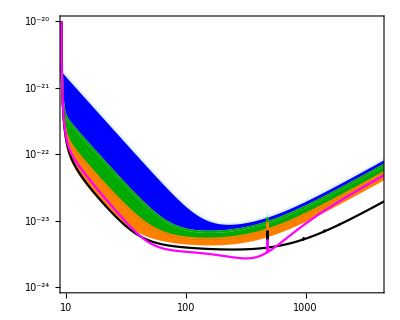

```mathematica
ListLogLogPlot[Table[Sn[detector],{detector,aLIGODetectors}],Joined->True,PlotRange->{{10^1,4*10^3},{10^-24,10^-20}},Frame->True,GridLines->Automatic,AspectRatio->0.8,Filling->{1->{{2},{Blue}},3->{{4},{Darker@Green}},5->{{6},{Orange}}},PlotStyle->{LightBlue,LightBlue,Darker@Green,Darker@Green,Orange,Orange,Black,Magenta}]
```

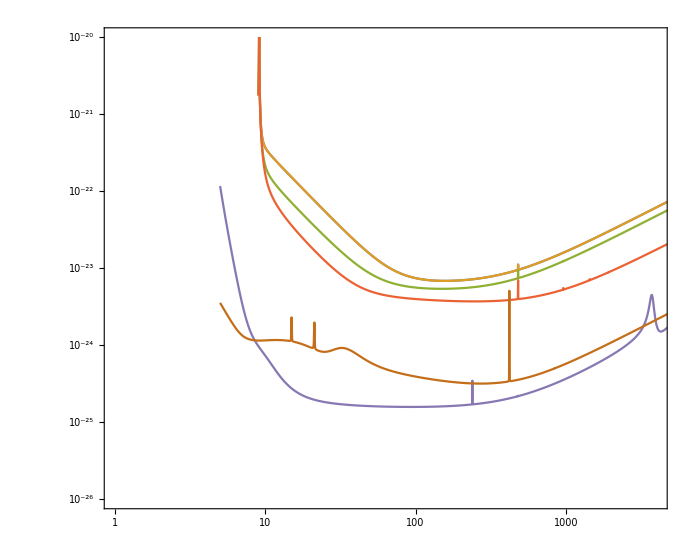

```mathematica
ListLogLogPlot[Table[Sn[detector],{detector,{"aLIGO_EARLY_HIGH","aLIGO_MID_LOW","aLIGO_MID_HIGH","aLIGO_DESIGN","CE","ET"}}],Joined->True,PlotRange->{{10^0,4*10^3},{10^-26,10^-20}},Frame->True,GridLines->Automatic,AspectRatio->0.8]
```

```mathematica
{"LIGO-P1200087-v18-AdV_BNS_OPTIMIZED.txt",
"LIGO-P1200087-v18-AdV_DESIGN.txt",
"LIGO-P1200087-v18-AdV_EARLY_HIGH.txt",
"LIGO-P1200087-v18-AdV_EARLY_LOW.txt", 
"LIGO-P1200087-v18-AdV_LATE_HIGH.txt",
"LIGO-P1200087-v18-AdV_LATE_LOW.txt", 
"LIGO-P1200087-v18-AdV_MID_HIGH.txt", 
"LIGO-P1200087-v18-AdV_MID_LOW.txt", 

"LIGO-P1200087-v18-aLIGO_BNS_OPTIMIZED.txt",
"LIGO-P1200087-v18-aLIGO_DESIGN.txt", 
"LIGO-P1200087-v18-aLIGO_EARLY_HIGH.txt", 
"LIGO-P1200087-v18-aLIGO_EARLY_LOW.txt", 
"LIGO-P1200087-v18-aLIGO_LATE_HIGH.txt", 
"LIGO-P1200087-v18-aLIGO_LATE_LOW.txt", 
"LIGO-P1200087-v18-aLIGO_MID_HIGH.txt", 
"LIGO-P1200087-v18-aLIGO_MID_LOW.txt",


"LIGO-P1600143-v18-CE_Pessimistic.txt", 
"LIGO-P1600143-v18-CE.txt", 
"LIGO-P1600143-v18-CE_Wideband.txt", 

"LIGO-P1600143-v18-ET_D.txt", 

"LIGO-T0900288-v3-BHBH_20deg.txt", 
"LIGO-T0900288-v3-High_Freq.txt", 

"LIGO-T0900288-v3-NO_SRM.txt", 
 "LIGO-T0900288-v3-NSNS_Opt.txt",

"LIGO-T0900288-v3-ZERO_DET_high_P.txt",
"LIGO-T0900288-v3-ZERO_DET_low_P.txt", 

"LIGO-T1600593-v1-KAGRA_Design.txt",
"LIGO-T1600593-v1-KAGRA_Early.txt",
 "LIGO-T1600593-v1-KAGRA_Late.txt",
"LIGO-T1600593-v1-KAGRA_Mid.txt",
"LIGO-T1600593-v1-KAGRA_Opening.txt"
}
```